```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.1,Jtwo,2*0.1,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.8660254037844387}]
```

{z→0.866025}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 p+4 J^2q*p+J^2 p^2))/(√(-4J*q-2J*p))/.{J->1,q->0.1,p->2*0.1}
```

0.866025+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.8660254037844387]]
```

{{0.005,0.869495},{0.01,0.872667},{0.015,0.875507},{0.02,0.877984},{0.025,0.880064},{0.03,0.881716},{0.035,0.882916},{0.04,0.883644},{0.045,0.883892},{0.05,0.883658},{0.055,0.882952},{0.06,0.881793},{0.065,0.880204},{0.07,0.878215},{0.075,0.875856},{0.08,0.87316},{0.085,0.870157},{0.09,0.866876},{0.095,0.863344},{0.1,0.859585}}

```mathematica
moduler[Lister[-1,-0.005,0.8660254037844387]]
```

{{-0.005,0.862288},{-0.01,0.85831},{-0.015,0.854117},{-0.02,0.84973},{-0.025,0.845169},{-0.03,0.840449},{-0.035,0.835585},{-0.04,0.830588},{-0.045,0.82547},{-0.05,0.820238},{-0.055,0.8149},{-0.06,0.809461},{-0.065,0.803928},{-0.07,0.798305},{-0.075,0.792594},{-0.08,0.7868},{-0.085,0.780924},{-0.09,0.774969},{-0.095,0.768935},{-0.1,0.762825}}

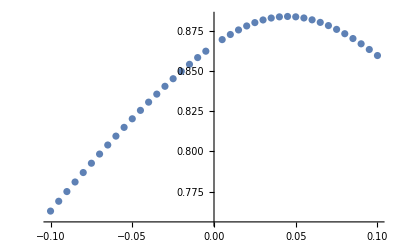

```mathematica
ListPlot[{{0.005,0.8694950646627286},{0.01,0.8726665057107106},{0.015,0.8755072973833385},{0.02,0.8779840097682964},{0.025,0.8800637666529293},{0.03,0.8817162436892646},{0.035,0.8829159282692178},{0.04,0.8836443192321675},{0.045,0.8838916629885397},{0.05,0.8836578589050668},{0.055,0.8829523350183853},{0.06,0.8817929401496878},{0.065,0.8802041207141426},{0.07,0.8782147657199633},{0.075,0.8758560891023608},{0.08,0.8731598129641855},{0.085,0.8701567809418873},{0.09,0.8668760172784051},{0.095,0.8633441757443228},{0.1,0.8595852917795701},{-0.005,0.8622878896834968},{-0.01,0.8583102081803914},{-0.015,0.854117098032372},{-0.02,0.8497303337123442},{-0.025,0.8451688666833486},{-0.03,0.8404490549510404},{-0.035,0.8355849314112553},{-0.04,0.8305884789048488},{-0.045,0.825469892930662},{-0.05,0.8202378219879928},{-0.055,0.8148995813625628},{-0.06,0.8094613397164568},{-0.065,0.8039282798277636},{-0.07,0.7983047358135674},{-0.075,0.7925943095416772},{-0.08,0.786799968955381},{-0.085,0.7809241308647066},{-0.09,0.7749687304988981},{-0.095,0.7689352798275242},{-0.1,0.7628249163749211}}]
```

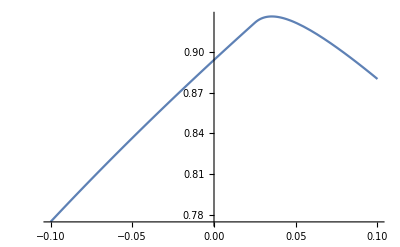

```mathematica
Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1}]
```